# Associated Mathematica file for Proulx and Teotonio “Weak selection of phenotypic memory in periodic environments”

This notebook creates figures and results in the paper.  Phenotypes and environmental optima are on the interval -1 to 1, fitness is Exp[-eta^2 (z-z*)^2], and lambda is per-generation asymptotic log growth. Evaluate the notebook from top to bottom. E

## Core model definitions

Here eta is the inverse width of the Gaussian fitness function: eta = 1/(Sqrt[2] sigma), so eta^2 = 1/(2 sigma^2). The environmental optima are -1 and 1. With row population vectors, selectionMatrix . transmissionMatrix implements selection followed by transmission.

```mathematica
ClearAll[zOpt,fitness,transmissionMatrix,selectionMatrix,cycleMatrix,dominantEigenvalue2,lambdaExpression,gradientExpression,secondZ2Expression,lambdaCompiled,gradientCompiled,secondZ2Compiled,lambdaNumeric,etaFromSigma,sigmaFromEta,logit,invLogit,periodicPhenotypeCycle,mutualInformation,binaryEntropy,maximumInformation,relativeInformation,numericalFirstDerivativeCheck,firstZDerivativeNumeric,makeFirstDerivativeSurface,secondZDerivativeNumeric,makeSecondDerivativeSurface,firstDerivativeSurface,secondDerivativeSurface,simulateTrajectory,evolveToEquilibrium,makeTrajectoryFigure,makeMemoryRegionPanel];
```

```mathematica
okabeIto=Apply[RGBColor,{{0,0,0},{0.9,0.6,0},{0.35,0.7,0.9},{0,0.6,0.5},{0.95,0.9,0.25},{0,0.45,0.7},{0.8,0.4,0},{0.8,0.6,0.7}},{1}];
```

```mathematica
etaFromSigma[s_?NumericQ]:=1/(√2 s);sigmaFromEta[x_?NumericQ]:=1/(√2 x);zOpt[1]=-1;zOpt[2]=1;fitness[z_,e_Integer,eta_]:=Exp[-eta^2 (z-zOpt[e])^2];
```

```mathematica
transmissionMatrix[beta1_,beta2_]:={{beta1,1-beta1},{1-beta2,beta2}};selectionMatrix[e_Integer,z1_,z2_,eta_]:=DiagonalMatrix[{fitness[z1,e,eta],fitness[z2,e,eta]}];cycleMatrix[z1_,z2_,beta1_,beta2_,eta_,k_Integer]:=Module[{b=transmissionMatrix[beta1,beta2],a1,a2},a1=selectionMatrix[1,z1,z2,eta].b;a2=selectionMatrix[2,z1,z2,eta].b;MatrixPower[a1,k].MatrixPower[a2,k]];
```

```mathematica
dominantEigenvalue2[m_]:=(Tr[m]+√(Tr[m]^2-4 Det[m]))/2;lambdaExpression[k_Integer]:=lambdaExpression[k]=Log[dominantEigenvalue2[cycleMatrix[z1,z2,beta1,beta2,eta,k]]]/(2 k);gradientExpression[k_Integer]:=gradientExpression[k]=(D[lambdaExpression[k],#1]&)/@{z1,z2,beta1,beta2};secondZ2Expression[k_Integer]:=secondZ2Expression[k]=D[lambdaExpression[k],{z2,2}]/.{z1->0,z2->0};
```

```mathematica
lambdaCompiled[k_Integer]:=lambdaCompiled[k]=With[{expr=lambdaExpression[k]},Compile[{{z1,_Real},{z2,_Real},{beta1,_Real},{beta2,_Real},{eta,_Real}},Evaluate[expr]]];gradientCompiled[k_Integer]:=gradientCompiled[k]=With[{expr=gradientExpression[k]},Compile[{{z1,_Real},{z2,_Real},{beta1,_Real},{beta2,_Real},{eta,_Real}},Evaluate[expr]]];secondZ2Compiled[k_Integer]:=secondZ2Compiled[k]=With[{expr=secondZ2Expression[k]},Compile[{{beta1,_Real},{beta2,_Real},{eta,_Real}},Evaluate[Re[expr]]]];lambdaNumeric[params_List,etaValue_?NumericQ,k_Integer]:=Module[{m=N[IdentityMatrix[2]],dominantRoot,b,a1,a2,scale,logScale=0.},b=transmissionMatrix[params⟦3⟧,params⟦4⟧];a1=N[selectionMatrix[1,params⟦1⟧,params⟦2⟧,etaValue].b];a2=N[selectionMatrix[2,params⟦1⟧,params⟦2⟧,etaValue].b];Do[m=m.a;scale=Max[Abs[Flatten[m]]];If[!TrueQ[scale>0.],Return[Indeterminate]];m=m/scale;logScale+=Log[scale],{a,Join[ConstantArray[a1,k],ConstantArray[a2,k]]}];dominantRoot=Max[Abs[Eigenvalues[m]]];If[!TrueQ[dominantRoot>0.],Return[Indeterminate]];(logScale+Log[dominantRoot])/(2 k)];
```

## Analytical results

The single-phenotype equilibrium is zero on the recoded scale. The randomizing-mutant calculation and all derivatives use log growth.

```mathematica
zHat=0;lambdaHat=-eta^2;lambdaRandomizing=1/2 1 (Log[beta fitness[zHat,1,eta]+(1-beta) fitness[zHat+eps,1,eta]]+Log[beta fitness[zHat,2,eta]+(1-beta) fitness[zHat+eps,2,eta]]);randomizingFirstDerivative=FullSimplify[D[lambdaRandomizing,eps]/.eps->0,Assumptions->eta>0∧0<beta<1];randomizingSecondDerivative=FullSimplify[D[lambdaRandomizing,{eps,2}]/.eps->0,Assumptions->eta>0∧0<beta<1];randomizingInvasionCondition=FullSimplify[randomizingSecondDerivative>0,Assumptions->eta>0∧0<beta<1];firstDerivativeChecks=Table[k->FullSimplify[{D[lambdaExpression[k],z1],D[lambdaExpression[k],z2]}/.{z1->0,z2->0},Assumptions->eta>0∧0<beta1<1∧0<beta2<1],{k,2,6}];
```

```mathematica
numericalFirstDerivativeCheck[k_Integer,samples_Integer:10000,seed_Integer:1234]:=Module[{epsValue=2/10^5,etaValue,b1,b2,derivative},SeedRandom[seed+k];Max[Table[etaValue=RandomReal[{(√2)/2,√2}];b1=RandomReal[];b2=RandomReal[];derivative=(lambdaNumeric[{epsValue,0.,b1,b2},etaValue,k]-lambdaNumeric[{-epsValue,0.,b1,b2},etaValue,k])/(2 epsValue);Abs[derivative],{samples}]]];longCycleChecks=<|20->numericalFirstDerivativeCheck[20],100->numericalFirstDerivativeCheck[100]|>;analyticResults=<|"SinglePhenotypeESS"->zHat,"SinglePhenotypeLogGrowth"->lambdaHat,"RandomizingFirstDerivative"->randomizingFirstDerivative,"RandomizingSecondDerivative"->randomizingSecondDerivative,"RandomizingInvasionCondition"->randomizingInvasionCondition,"GeneralFirstDerivativeChecks"->firstDerivativeChecks,"LongCycleNumericalChecks"->longCycleChecks|>;
```

```mathematica
analyticResults
```

<|SinglePhenotypeESS→0,SinglePhenotypeLogGrowth→-eta^2,RandomizingFirstDerivative→0,RandomizingSecondDerivative→-2 (-1+beta) eta^2 (-1+2 beta eta^2),RandomizingInvasionCondition→2 beta eta^2>1,GeneralFirstDerivativeChecks→{2→{0,0},3→{0,0},4→{0,0},5→{0,0},6→{0,0}},LongCycleNumericalChecks→<|20→7.21645×10^-11,100→5.10703×10^-10|>|>

## Second-derivative surface over transmission parameters

This section estimates the second derivative of per-generation log growth with respect to either phenotype at z1 = z2 = 0. It compares log growth at a small positive change, no change, and an equal negative change. Positive values indicate that small phenotypic deviations can increase log growth, whereas negative values indicate local stabilizing selection. The beta endpoints are omitted because the transmission matrix becomes reducible there.

```mathematica
secondZDerivativeNumeric[which_Integer,beta1Value_?NumericQ,beta2Value_?NumericQ,etaValue_?NumericQ,k_Integer,epsValue_:1/10^3]:=Module[{base={0.,0.,beta1Value,beta2Value},plus={0.,0.,beta1Value,beta2Value},minus={0.,0.,beta1Value,beta2Value},lambdaBase},If[!MemberQ[{1,2},which],Return[$Failed]];plus⟦which⟧=epsValue;minus⟦which⟧=-epsValue;lambdaBase=lambdaNumeric[base,etaValue,k];(lambdaNumeric[plus,etaValue,k]-2 lambdaBase+lambdaNumeric[minus,etaValue,k])/epsValue^2];makeSecondDerivativeSurface[which_Integer,k_Integer,etaValue_?NumericQ,epsValue_:1/10^3]:=Module[{verticalLabel=If[which==1,"d^2 lambda/d z1^2","d^2 lambda/d z2^2"],title="k = "<>ToString[k]<>", eta^2 = "<>ToString[N[etaValue^2]]},If[!MemberQ[{1,2},which],Return[$Failed]];Plot3D[secondZDerivativeNumeric[which,beta1Plot,beta2Plot,etaValue,k,epsValue],{beta1Plot,0.001,0.999},{beta2Plot,0.001,0.999},PlotPoints->45,MaxRecursion->2,Mesh->None,PlotRange->{0,1},ColorFunction->"LakeColors",AxesLabel->{Subscript[β, 1],Subscript[β, 2],verticalLabel},PlotLabel->title,ImageSize->520]];
```

```mathematica
secondDerivativeSurfaceK=6;secondDerivativeSurfaceEta=1.;secondDerivativeSurfacePhenotype=1;secondDerivativeSurface=makeSecondDerivativeSurface[secondDerivativeSurfacePhenotype,secondDerivativeSurfaceK,secondDerivativeSurfaceEta];
```

```mathematica
secondDerivativeSurface
```

-Graphics3D-

## Invasion regions for small phenotypic differences

The randomization plot uses eta^2 as the mismatch-strength axis. To preserve the existing calls to makeMemoryRegionPanel, that function accepts the old 0-to-1-scale coefficient values and internally uses eta = Sqrt[oldStrength]/2; displayed labels report eta^2 = oldStrength/4.

```mathematica
randomizationRegionFigure=RegionPlot[etaSquaredPlot betaPlot>1/2,{etaSquaredPlot,1/2,5/2},{betaPlot,0,1},Frame->True,FrameLabel->{"Mismatch strength, η^2",β},PlotPoints->60,MaxRecursion->2,ImageSize->420];
```

```mathematica
makeMemoryRegionPanel[k_Integer,oldStrengthValues_List,panelLabel_String,etaLabelPositions_List]:=Module[{colors,positiveQ,plots,etaLabels},colors={Directive[okabeIto⟦3⟧,Opacity[1]],Directive[okabeIto⟦2⟧,Opacity[0.6]],Directive[okabeIto⟦4⟧,Opacity[0.6]]};positiveQ[beta2_?NumericQ,beta1_?NumericQ,oldStrength_?NumericQ]:=secondZ2Compiled[k][beta1,beta2,(√N[oldStrength])/2]>0;plots=MapThread[Function[{oldStrength,color},RegionPlot[positiveQ[beta2Plot,beta1Plot,oldStrength],{beta2Plot,0,1},{beta1Plot,0,1},PlotStyle->color,BoundaryStyle->None,PlotPoints->50,MaxRecursion->2]],{oldStrengthValues,colors}];etaLabels=(Inset[Style["η^2 = "<>ToString[N[(#1⟦1⟧)/4]],11,Black],#1⟦2⟧]&)/@etaLabelPositions;Show[plots,Frame->True,FrameLabel->{Subscript[β, 2],Subscript[β, 1]},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[0.02],Epilog->Join[etaLabels,{Inset[Style[panelLabel,14,Bold],Scaled[{0.95,0.95}]],Inset[Style["k = "<>ToString[k],12],Scaled[{0.86,0.08}]]}],ImagePadding->{{45,12},{40,12}},ImageSize->360]];
```

```mathematica
memoryRegionFigure=GraphicsRow[{makeMemoryRegionPanel[2,{4,3,2.5},"A",{{2.5,{0.12,0.93}},{3,{0.3,0.75}},{4,{0.42,0.58}}}],makeMemoryRegionPanel[6,{3,2.5,2},"B",{{2,{0.55,0.93}},{2.5,{0.55,0.73}},{3,{0.55,0.63}}}]},Spacings->10,ImageSize->850];
```

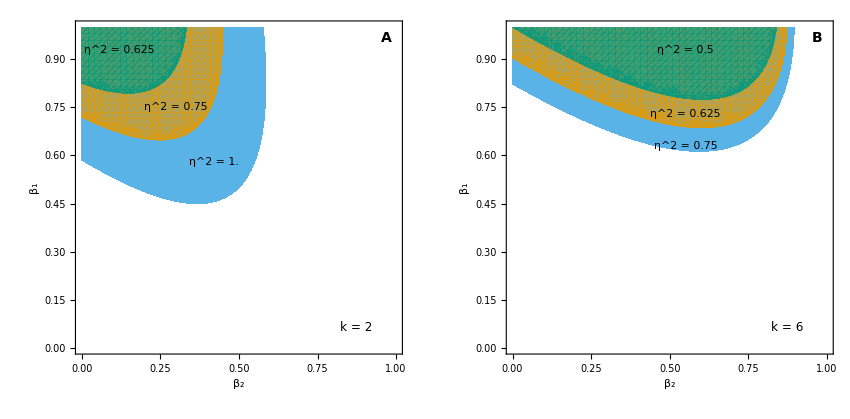

```mathematica
memoryRegionFigure
```

## Established memory system

This section now reports log growth. The comparison uses eta^2 = 1/2, which is equivalent to the old coefficient 2 after doubling the phenotype scale.

```mathematica
lambdaExtreme[beta1_,beta2_,k_]:=((k-1) Log[beta1]+Log[1-beta1]+(k-1) Log[beta2]+Log[1-beta2])/(2 k);optimalMemory[k_]:=(k-1)/k;optimalExtremeLogGrowth[k_]:=FullSimplify[lambdaExtreme[optimalMemory[k],optimalMemory[k],k],Assumptions->k>1];establishedMemoryResults=<|"OptimalMemory"->(k-1)/k,"OptimalPerGenerationLogGrowth"->(k-1)/k Log[k-1]-Log[k]|>;establishedMemoryFigure=Plot[{(kValue-1)/kValue Log[kValue-1]-Log[kValue],-1/2},{kValue,2,20},Frame->True,FrameLabel->{"Environmental run length, k","Per-generation log growth, λ"},PlotLegends->{"Established memory system","Single-phenotype equilibrium, η^2 = 1/2"},PlotRange->All,ImageSize->480];
```

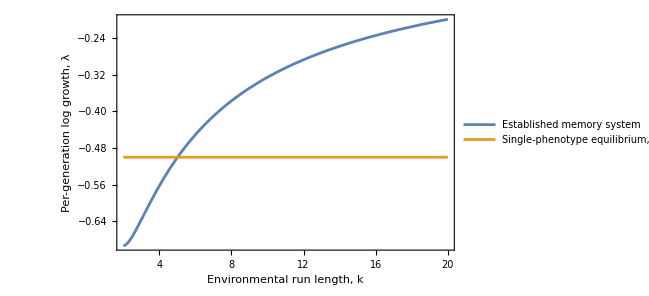

```mathematica
establishedMemoryFigure
```

## Mutual information

```mathematica
periodicPhenotypeCycle[params_List,etaValue_?NumericQ,k_Integer]:=Module[{m,eigensystem,index,state,env,states,pairedEnv,b},m=N[cycleMatrix[Sequence@@params,etaValue,k]];eigensystem=Eigensystem[Transpose[m]];index=First[Ordering[Re[eigensystem⟦1⟧],-1]];state=Abs[Re[eigensystem⟦2,index⟧]];state=state/Total[state];b=transmissionMatrix[params⟦3⟧,params⟦4⟧];env=Join[ConstantArray[1,k],ConstantArray[2,k]];states=Table[state=state.selectionMatrix[e,params⟦1⟧,params⟦2⟧,etaValue].b;state=state/Total[state];state,{e,env}];pairedEnv=RotateLeft[env];<|"Environment"->pairedEnv,"PhenotypeFrequencies"->states|>];mutualInformation[params_List,etaValue_?NumericQ,k_Integer]:=Module[{cycle,env,states,joint,pEnv,pPhen,term},cycle=periodicPhenotypeCycle[params,etaValue,k];env=cycle["Environment"];states=cycle["PhenotypeFrequencies"];joint=Table[Total[Table[If[env⟦t⟧==e,states⟦t,i⟧,0],{t,Length[env]}]]/Length[env],{e,1,2},{i,1,2}];pEnv=Total/@joint;pPhen=Total[joint];term[x_,y_]:=If[x≤0,0,x Log[2,x/y]];Sum[term[joint⟦e,i⟧,pEnv⟦e⟧ pPhen⟦i⟧],{e,1,2},{i,1,2}]];binaryEntropy[x_?NumericQ]:=If[x≤0∨x≥1,0,-x Log[x]/Log[2]-(1-x) Log[2,1-x]];maximumInformation[k_Integer]:=1-binaryEntropy[1/k];relativeInformation[params_List,etaValue_?NumericQ,k_Integer]:=mutualInformation[params,etaValue,k]/maximumInformation[k];
```

## Evolutionary simulation

The phenotype coordinates use the shifted logit Log[(1+z)/(1-z)] with inverse 2/(1+Exp[-x])-1. Retention probabilities continue to use the ordinary 0-to-1 logit. No rescaled phenotype vector is introduced. Because the new phenotype coordinate is twice as wide, the two phenotype components of the evolutionary gradient are multiplied by two for update ranking, convergence, and step size; this keeps those numerical operations invariant to the change of coordinates.

```mathematica
logit[x_?NumericQ,index_Integer]:=If[index≤2,Log[(1+x)/(1-x)],Log[x/(1-x)]];invLogit[x_?NumericQ,index_Integer]:=If[index≤2,2/(1+Exp[-x])-1,1/(1+Exp[-x])];
```

```mathematica
simulateTrajectory[k_Integer,etaValue_?NumericQ,initialParameters_List,tolerance_:1/10^4,stepSize_:1.,maxSteps_Integer:10000]:=Module[{params=N[initialParameters],gradFun,lamFun,grad,effectiveGradient,index,records={},step=0,lam,info,maxGradient},gradFun=gradientCompiled[k];lamFun=lambdaCompiled[k];While[step≤maxSteps,grad=N[gradFun@@Join[params,{etaValue}]];effectiveGradient=grad {2.,2.,1.,1.};lam=N[lamFun@@Join[params,{etaValue}]];info=If[k>2,N[relativeInformation[params,etaValue,k]],Indeterminate];maxGradient=Max[Abs[effectiveGradient]];AppendTo[records,Join[{step},params,{lam,Norm[effectiveGradient],info}]];If[maxGradient≤tolerance∨step==maxSteps,Break[]];index=First[Ordering[Abs[effectiveGradient],-1]];params⟦index⟧=invLogit[logit[params⟦index⟧,index]+stepSize effectiveGradient⟦index⟧,index];step++;Null];<|"Columns"->{"Step","z1","z2","beta1","beta2","lambda","EvolutionaryGradientNorm","RelativeInformation"},"Data"->records,"FinalParameters"->params,"Steps"->step|>];
```

```mathematica
makeTrajectoryFigure[result_Association,k_Integer]:=Module[{data=result["Data"],phenotypePlot,memoryPlot,gradientPlot,informationPlot},phenotypePlot=ListLinePlot[{data⟦All,{1,2}⟧,data⟦All,{1,3}⟧},Frame->True,FrameLabel->{"Evolutionary step","Phenotypic value"},PlotRange->{All,{-1,1}},Epilog->{Inset[Style["A",16,Bold],Scaled[{0.9,0.92}]]},ImageSize->380];memoryPlot=Show[ListLinePlot[{data⟦All,{1,4}⟧,data⟦All,{1,5}⟧},Frame->True,FrameLabel->{"Evolutionary step","Retention probability"},PlotRange->{All,{0,1}},Epilog->{Inset[Style["B",16,Bold],Scaled[{0.9,0.92}]]},ImageSize->380],Plot[1-1/k,{x,First[data⟦All,1⟧],Last[data⟦All,1⟧]},PlotStyle->Dashed]];gradientPlot=ListLinePlot[data⟦All,{1,7}⟧,Frame->True,FrameLabel->{"Evolutionary step","Log-growth gradient"},PlotRange->All,Epilog->{Inset[Style["C",16,Bold],Scaled[{0.9,0.92}]]},ImageSize->380];informationPlot=ListLinePlot[data⟦All,{1,8}⟧,Frame->True,FrameLabel->{"Evolutionary step","Relative information"},PlotRange->{All,{0,1}},Epilog->{Inset[Style["D",16,Bold],Scaled[{0.9,0.92}]]},ImageSize->380];GraphicsGrid[{{phenotypePlot,memoryPlot},{gradientPlot,informationPlot}},Spacings->{0.5,0.5},ImageSize->800]];
```

```mathematica
mainK=6;mainEtaSquared=0.75;mainEta=√mainEtaSquared;mainInitialParameters={0.,0.1,0.99,0.01};mainTrajectory=simulateTrajectory[mainK,mainEta,mainInitialParameters,1/10^4,1.,10000];trajectoryFigure=makeTrajectoryFigure[mainTrajectory,mainK];
```

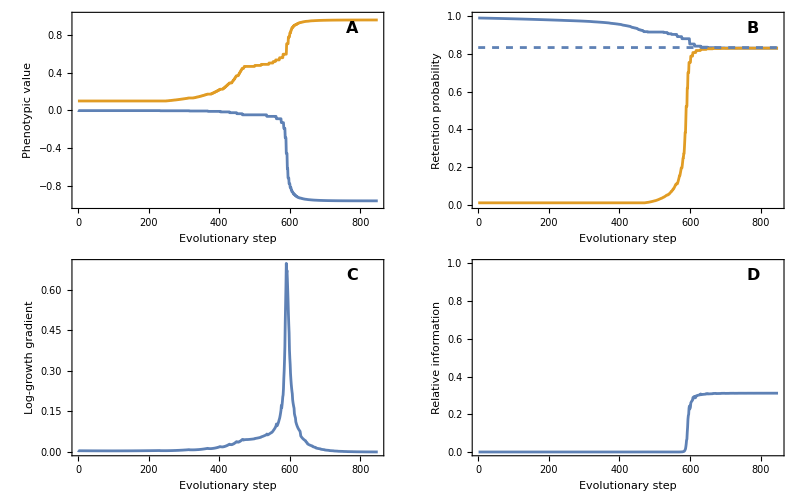

```mathematica
trajectoryFigure
```

## Origin versus maintenance: hysteresis

The scan is expressed directly in eta^2. Each call to the evolutionary routine receives eta = Sqrt[etaSquared]. The phenotype starting values, collapse criterion, and vertical plotting scale have all been doubled relative to the old 0-to-1 phenotype coordinate.

```mathematica
evolveToEquilibrium[k_Integer,etaValue_?NumericQ,startingParameters_List,tolerance_:1/10^4,stepSize_:1.,maximumSteps_Integer:30000]:=Module[{parameters=N[startingParameters],gradientFunction=gradientCompiled[k],gradient,effectiveGradient,parameterToChange,step=0},While[step<maximumSteps,gradient=N[gradientFunction[parameters⟦1⟧,parameters⟦2⟧,parameters⟦3⟧,parameters⟦4⟧,etaValue]];effectiveGradient=gradient {2.,2.,1.,1.};If[Max[Abs[effectiveGradient]]≤tolerance,Break[]];parameterToChange=First[Ordering[Abs[effectiveGradient],-1]];parameters⟦parameterToChange⟧=invLogit[logit[parameters⟦parameterToChange⟧,parameterToChange]+stepSize effectiveGradient⟦parameterToChange⟧,parameterToChange];step++;Null];<|"FinalParameters"->parameters,"Steps"->step|>];
```

```mathematica
hysteresisK=6;etaSquaredValues=N[Append[Range[1/8,79/80,3/80],1]];noMemoryStartingParameters={0.,0.1,0.99,0.01};originData=Module[{parameters=noMemoryStartingParameters,result},Table[If[Abs[parameters⟦1⟧]<0.1∨Abs[parameters⟦2⟧]<0.1,parameters=noMemoryStartingParameters];result=evolveToEquilibrium[hysteresisK,√etaSquared,parameters,1/10^4,1.,30000];parameters=result["FinalParameters"];{etaSquared,parameters⟦1⟧,parameters⟦2⟧,parameters⟦3⟧,parameters⟦4⟧,result["Steps"]},{etaSquared,etaSquaredValues}]];maintenanceData=Module[{parameters=noMemoryStartingParameters,result},Table[result=evolveToEquilibrium[hysteresisK,√etaSquared,parameters,1/10^4,1.,30000];parameters=result["FinalParameters"];{etaSquared,parameters⟦1⟧,parameters⟦2⟧,parameters⟦3⟧,parameters⟦4⟧,result["Steps"]},{etaSquared,Reverse[etaSquaredValues]}]];
```

```mathematica
hysteresisFigure=Show[ListPlot[{({#1⟦1⟧,Max[0.1,Abs[#1⟦2⟧-#1⟦3⟧]]}&)/@originData},Frame->True,FrameLabel->{η^2,"Difference in phenotype"},PlotMarkers->{Style["■",20,okabeIto⟦8⟧,Opacity[0.9965000000000001]]},PlotRange->{All,{-0.1,2.1}},ImageSize->520],ListPlot[{({#1⟦1⟧,0.0102+Max[0.1,Abs[#1⟦2⟧-#1⟦3⟧]]}&)/@maintenanceData},Frame->True,FrameLabel->{η^2,"Difference in phenotype"},PlotMarkers->{Style["▲",20,okabeIto⟦3⟧,Opacity[0.49]]},PlotRange->{All,{-0.1,2.1}},ImageSize->520]];
```

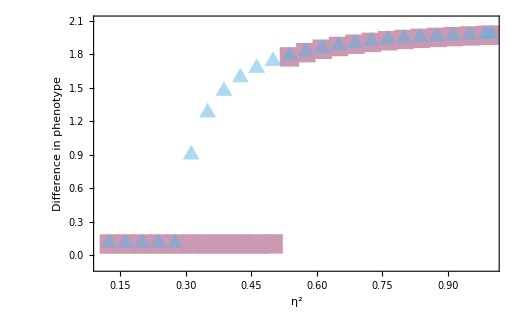

```mathematica
hysteresisFigure
```

### Compare to DME

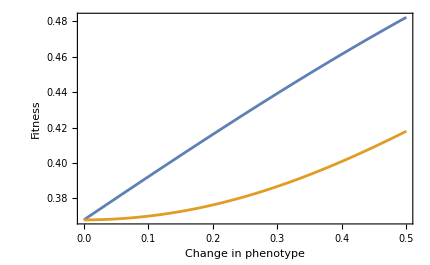

```mathematica
ClearAll[dmeLogGrowth,stateLogGrowth,dmeComparisonFigure];

(*Figure parameters*)
kValue=6;

etaValue=1;          (*eta^2=1*)
beta1Value=5/6;       (*state-retention probabilities*)
beta2Value=5/6;
epsilonMaximum=0.5;

lambdaAncestor=-etaValue^2;

(*Deterministic maternal effect:equation dme-growth*)
dmeLogGrowth[eps_?NumericQ]:=-etaValue^2 ((kValue-1)/kValue (1-eps/2)^2+1/kValue (1+eps/2)^2);

(*State-transmission mutant with phenotypes {0,+epsilon}*)
stateLogGrowth[eps_?NumericQ]:=lambdaNumeric[{-eps/2,eps/2,beta1Value,beta2Value},etaValue,kValue];

dmeColor=RGBColor[0.80,0.20,0.15];
stateColor=RGBColor[0.00,0.45,0.70];

dmeComparisonFigure=Plot[{dmeLogGrowth[eps],stateLogGrowth[eps]},{eps,0,epsilonMaximum},Frame->True,Axes->False,FrameLabel->{"Phenotypic perturbation, ϵ","Per-generation log growth, λ"},PlotStyle->{Directive[dmeColor,AbsoluteThickness[2.5]],Directive[stateColor,AbsoluteThickness[2.5]]},PlotLegends->Placed[LineLegend[{dmeColor,stateColor},{"Deterministic maternal effect","State transmission"}],{0.68,0.22}],GridLines->{None,{lambdaAncestor}},GridLinesStyle->Directive[GrayLevel[0.5],Dashed],PlotRange->All,PlotRangePadding->Scaled[0.04],PlotPoints->80,MaxRecursion->2,ImageSize->430,BaseStyle->{FontFamily->"Helvetica",12}];

dmeComparisonFigure=Plot[{Exp[dmeLogGrowth[eps]],Exp[stateLogGrowth[eps]]},{eps,0,epsilonMaximum},Frame->True,FrameLabel->{"Change in phenotype","Fitness"},ImageSize->430,BaseStyle->{FontFamily->"Helvetica",12}];

dmeComparisonFigure
```

### Analytic results for the derivative of the eigenvalues

#### Model and parameters

```mathematica
b={{beta1,1-beta1},{1-beta2,beta2}};
betaAssumptions=Element[{beta1,beta2},Reals]&&0<beta1<1&&0<beta2<1;
parameterRules=First[Solve[Join[Thread[{q1,q2}.b=={q1,q2}],{q1+q2==1,h==beta1+beta2-1}],{beta1,beta2,q1}]];
b=Simplify[b/.parameterRules];
assumptions=Element[{eta,h,q2,x},Reals]&&eta>0&&-1<h<1&&0<q2<1&&Element[k,Integers]&&k>=1&&(And@@(0<#<1&/@Flatten[b]));
w[e_,z_]:=DiagonalMatrix[{Exp[-eta^2],Exp[-eta^2*(e-z)^2]}];
```

#### Cycle and ancestral growth

```mathematica
cycle=MatrixPower[w[-1,x].b,k].MatrixPower[w[1,x].b,k];
polynomial=CharacteristicPolynomial[cycle,y];
characteristic=polynomial/.y->Exp[2*k*lambda[x]];
lambda0=FullSimplify[Log[Max@@Eigenvalues[w[-1,0].b]],assumptions]
```

-eta^2

#### Log-growth derivatives

```mathematica
rule0={lambda[0]->lambda0};
firstDerivative=FullSimplify[(D[characteristic,x]/.x->0)/.rule0,assumptions];
rule1=First[Solve[firstDerivative==0,Derivative[1][lambda][0]]];
secondDerivative=FullSimplify[(D[characteristic,{x,2}]/.x->0)/.Join[rule0,rule1],assumptions];
rule2=First[Solve[secondDerivative==0,Derivative[2][lambda][0]]];
lambda2=FullSimplify[Derivative[2][lambda][0]/.rule2,assumptions]
```

-2 eta^2 q2+(4 eta^4 (-k+h (4+h k)+h^k (-4 h+(-1+h^2) k)) (-1+q2) q2)/((-1+h)^2 (1+h^k) k)

#### Compact form

```mathematica
short=FullSimplify[lambda2/.{h^(2*k)->u^2,h^k->u},assumptions&&Element[u,Reals]&&-1<u<1];
compact=Collect[short,eta,Factor]/.u->h^k;
compact
```

-2 eta^2 q2+(4 eta^4 (4 h-4 h^(1+k)-k+h^2 k-h^k k+h^(2+k) k) (-1+q2) q2)/((-1+h)^2 (1+h^k) k)

Which is equivalent to the expression that we present

```mathematica
typesetForm = 2 eta^2 q2 (-1 + 2 eta^2 (1 - q2)
  ((1 + h)/(1 - h) - 4 h (1 - u)/(k (1 - h)^2 (1 + u))));
```

```mathematica
Simplify[typesetForm-compact/.{u->h^k}//Expand]
```

0